Stochastic simulation for the storage effect in the model of minimum iteroparity, with Young and Old demes

```mathematica
Rep=4; (* number of replicates *)
SamplInt = 20; (* time interval between sampling allele frequency *)
Cap=10000; (* the baseline carrying capacity for Y deme: K0 *)
senv =0.14; sran=0.02; (* parameers for fitness fluctuation: senv = a_S, sran = b_S *)
sdel=0; (* relative reduction of fitness during favorable environments - for net deleterious mutations *)
yenv=0.2; yran=0.1;  (* parameters for demographic fluctuation: yenv = a_X, yran = b_X *)

dregul=1000; (* dregul is parameter g in Kim (2023) a large positive value sets soft selection (strong density regulation) *)
Lseq=1; (* the number of loci *)
NSelSite=1;  (* the number of loci under selection; as this study does not include neutral loci, you need to set Lseq = NSelSite *)
selco=Table[{0,1},{l,1,NSelSite}];
selco=Join[selco,Table[{0,0},{l,1,Lseq-NSelSite}]];
beta=1.2; (* the fecundity of old adults relative to young adults: b *)
rmut=0.000005; (* mutation rate per locus per generation: mu *)
eY=0.8;(* probability for a haploid advancing from the young to old stage: r *)
TotGen=100000; (* maximum length (generation) of a single simulation run *)
intvl=20000;
cvlist={};
mTfix = {};
mfixed=Table[0,{l,1,NSelSite}];
nfixed=0;
mmHetList={};
FreqList={};

For[rep=0,rep<Rep,rep++;
NPopTraj={};
fini=If[Mod[rep,2]==0,0.05,0.95]; (* intial frequency of the A2 allele, alternating between 0.05 and 0.95 *)
PYng={Cap fini, (1-fini)Cap}; 
HYng={0,1}; (* HYng = haplotype list, PYng = corresponding number (>0) of individuals in deme Y *)
POld={Cap eY fini,Cap eY(1-fini)};HOld={0,1}; (* number and haplotype lists in deme O *)

mHetTraj={};
gen=0;
AF=mHet=Table[0,{l,1,Lseq}];
mmHet=0;
m01=m15=m59=m910=0;

While[
gen<TotGen,
gen++;

env=RandomVariate[NormalDistribution[]]; (* sampling the environment (Z1) *)
es=env;
For[site=0,site<Lseq,site++; If[env>0,es*=1-sdel]];
wlist=AMFfitRF[es,senv, sran, selco,Lseq]; (* assigning the fitness of A2. a_S*(1-d)*Z1 + b_S*Z2 if Z1>0 and a_S*Z1 + b_S*Z2 if Z1<0 *)

{PGmt,HGmt}=MergePops[PYng,HYng,beta POld,HOld]; (* combining Y and O adults of previous year before reproduction in deme Y *)
HFitY=HaploFit[HGmt, wlist,Lseq]; 

KYoung=Cap Exp[yenv env+yran RandomVariate[NormalDistribution[]]];  (* assigning the carrying capacity of Y deme: K_t *)
{POffs,HOffs}=PoissonReproduceRF[PGmt, HGmt,HFitY, KYoung, dregul];(* Reproduction in deme Y *)

{POffs,HOffs}=Mutation[POffs,HOffs, rmut Lseq, Lseq]; (* Mutation step Y *)


{POld,HOld}=Advance[PYng,HYng,eY]; (* Formaing deme O from deme Y *)
{PYng,HYng}={POffs,HOffs}; (* New deme Y *)

NY=Total[PYng];nHY=Length[PYng];
NO=Total[POld];nHO=Length[POld];
If[(NY==0)||(NO==0),Print["Extinct ",{gen,NY,NO}];Break[]];

YFreq=Table[Count1[PYng,HYng,nHY,st],{st,1,Lseq}]; (* counting mutant frequencies at all loci in deme Y *)
OFreq=Table[Count1[POld,HOld,nHO,st],{st,1,Lseq}];

For[site=0,site<Lseq,site++;
AF[[site]]=1.0(YFreq[[site]]+OFreq[[site]])/(NY+NO); (* allele frequency in the entire population *)
mHet[[site]]+=2AF[[site]](1-AF[[site]]); (* expected heterozygosity *)
If[AF[[site]]<0.1, m01++,
If[AF[[site]]<0.5,m15++,If[AF[[site]]<0.9,m59++, m910++]] ]; (* to record the proportion of times the frequency stays in [0, 0.1), [0.1, 0.5), [0.5, 0.9), and [0.9, 1] *)
If[Mod[gen,SamplInt]==0,FreqList=Append[FreqList,AF[[site]]]]
];

If[Mod[gen,intvl]==0,
Print[gen, AF,{NY, NO}]
]
];

For[site=0,site<Lseq,site++;
mHet[[site]]/=gen;
mmHet +=mHet[[site]]/Lseq;
];
mmHetList=Append[mmHetList,mmHet];
m01/=(Lseq gen);m15/=(Lseq gen); m59/=(Lseq gen);m910/=(Lseq gen);
If[senv >0 || sran>0,Phi=senv yenv/(senv^2+sran^2),Phi=0];
Print[rep," Phi= ",Phi," 1/(2r)= ",0.5/eY, " het=",mmHet," p[0,0.1]=",1.0 m01," p[0.1,0.5]=", 1.0 m15," p[0.5,0.9]=",1.0m59, " p[0.9,1]=",1.0m910]
];
Print[{Mean[mmHetList],StandardDeviation[mmHetList],Mean[FreqList],StandardDeviation[FreqList]}];
midfr=0; LL=Length[FreqList];For[i=0,i<LL,i++;If[Between[FreqList[[i]],{0.1,0.9}],midfr++]](* counting mutant frequencies at all loci in deme Y *) 
midfr/LL//N
```

20000{0.}{11573,10038}

40000{0.0000736703}{7715,5859}

60000{0.000439947}{9344,6567}

80000{0.808007}{8967,5096}

100000{0.}{8766,6759}

1 Phi= 1.4 1/(2r)= 0.625 het=0.0862796 p[0,0.1]=0.76257 p[0.1,0.5]=0.1255 p[0.5,0.9]=0.08851 p[0.9,1]=0.02342

20000{0.00031407}{12093,7011}

40000{0.996603}{7954,11180}

60000{1.}{9025,9701}

80000{1.}{6773,8812}

100000{1.}{8267,6259}

2 Phi= 1.4 1/(2r)= 0.625 het=0.00657711 p[0,0.1]=0.38452 p[0.1,0.5]=0.00628 p[0.5,0.9]=0.00553 p[0.9,1]=0.60367

20000{0.}{10859,10073}

40000{1.}{6832,10416}

60000{1.}{9493,6347}

80000{0.999916}{16787,6931}

100000{1.}{9818,13357}

3 Phi= 1.4 1/(2r)= 0.625 het=0.016876 p[0,0.1]=0.27289 p[0.1,0.5]=0.01227 p[0.5,0.9]=0.02672 p[0.9,1]=0.68812

20000{1.}{13628,6154}

40000{0.}{8508,8654}

60000{0.257501}{11941,8389}

80000{0.}{7326,8304}

100000{0.}{11255,8330}

4 Phi= 1.4 1/(2r)= 0.625 het=0.103744 p[0,0.1]=0.38213 p[0.1,0.5]=0.09067 p[0.5,0.9]=0.15475 p[0.9,1]=0.37245

{0.0533692,0.0487919,0.488476,0.472417}

0.12725

```mathematica
Lrun=TotGen/SamplInt
```

5000

```mathematica
FRun[rep_]:=Table[{20 t,FreqList[[(rep-1)Lrun+k+(t-1) Lseq]]},{k,1,Lseq}, {t,1,Lrun}];
```

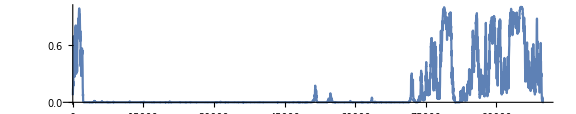

```mathematica
gRun1=ListPlot[FRun[1],Joined->True,AspectRatio->0.2,PlotRange->{0,1},ImageSize->Large]
```

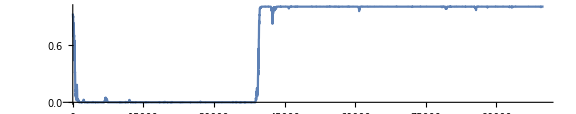

```mathematica
gRun2=ListPlot[FRun[2],Joined->True,AspectRatio->0.2,PlotRange->{0,1},ImageSize->Large]
```

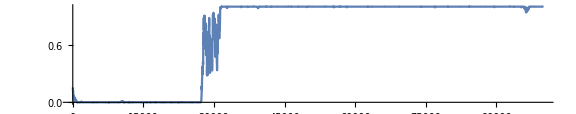

```mathematica
gRun3=ListPlot[FRun[3],Joined->True,AspectRatio->0.2,PlotRange->{0,1},ImageSize->Large]
```

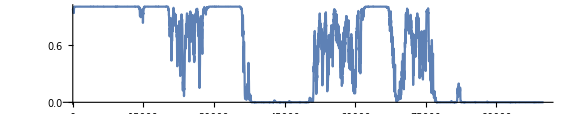

```mathematica
gRun4=ListPlot[FRun[4],Joined->True,AspectRatio->0.2,PlotRange->{0,1},ImageSize->Large]
```